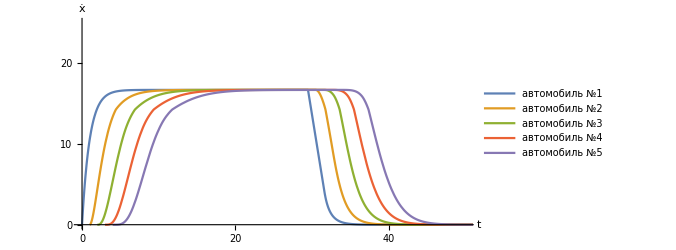

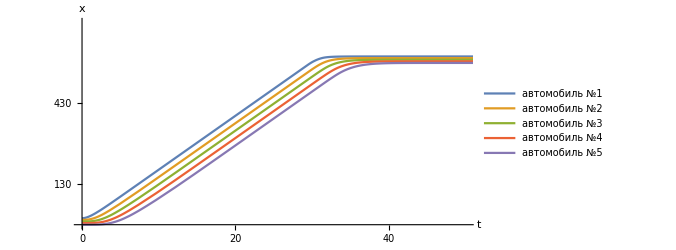

speed.pdf

path.pdf

```mathematica
speed =Module[{e},
tmax =120;
Subscript[V, max] =60*10/36;
vm=0;
τ = 1;
λ=5;
a=1;
q=1;
l=2;


Q[x1_,x2_,v_] := If[x1-x2 < (v^2)/(2*0.6*9.8)+2, 0,1];
QQ[x1_,x2_,v_] := If[x1-x2 <= (v^2)/(2*0.6*9.8)+2, 1,0];
Module[{},

solF= NDSolve[{u''[t]== Q[500,u[t],u'[t]]* a *(Subscript[V, max]-u'[t])+
q*QQ[500,u[t],u'[t]]*(( (u'[t]^2*(-u'[t]+vm)))/(500-u[t])^2)
, u[t /; t≤ 0] == 0, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
solS = NDSolve[{v''[t]==Q[Evaluate[u[t-τ] /.solF][[1]], v[t],v'[t]]*a*(
Evaluate[u'[t-τ] /.solF][[1]]-v'[t])+
q*QQ[Evaluate[u[t-τ] /.solF][[1]],v[t],v'[t]]*(( (v'[t]^2*(-v'[t]+Evaluate[u'[t-τ] /.solF][[1]])))/(Evaluate[u[t-τ] /.solF][[1]]-v[t]-l)^2)
, v[t /; t≤ τ ] == -1*λ, v'[t /; t≤ τ ] == 0},v,{t,τ,tmax}];

solT = NDSolve[{w''[t]==Q[Evaluate[v[t-τ] /.solS][[1]], w[t],w'[t]]*a*(
Evaluate[v'[t-τ] /.solS][[1]]-w'[t])+
q*QQ[Evaluate[v[t-τ] /.solS][[1]],w[t],w'[t]]*(( (w'[t]^2*(-w'[t]+Evaluate[v'[t-τ] /.solS][[1]])))/(Evaluate[v[t-τ] /.solS][[1]]-w[t]-l)^2)
, w[t /; t≤ 2*τ ] == -2*λ, w'[t /; t≤ 2*τ ] == 0},w,{t,2*τ,tmax}];

sol4 = NDSolve[{p''[t]==Q[Evaluate[w[t-τ] /.solT][[1]], p[t],p'[t]]*a*(
Evaluate[w'[t-τ] /.solT][[1]]-p'[t])+
q*QQ[Evaluate[w[t-τ] /.solT][[1]],p[t],p'[t]]*(( (p'[t]^2*(-p'[t]+Evaluate[w'[t-τ] /.solT][[1]])))/(Evaluate[w[t-τ] /.solT][[1]]-p[t]-l)^2)
,p[t /; t≤ 3*τ ] == -3*λ, p'[t /; t≤ 3*τ ] == 0},p,{t,3*τ,tmax}];

sol5 = NDSolve[{z''[t]==Q[Evaluate[p[t-τ] /.sol4][[1]], z[t],z'[t]]*a*(
Evaluate[p'[t-τ] /.sol4][[1]]-z'[t])+
q*QQ[Evaluate[p[t-τ] /.sol4][[1]],z[t],z'[t]]*(( (z'[t]^2*(-z'[t]+Evaluate[p'[t-τ] /.sol4][[1]])))/(Evaluate[p[t-τ] /.sol4][[1]]-z[t]-l)^2)
,z[t /; t≤ 4*τ ] == -4*λ, z'[t /; t≤ 4*τ ] == 0},z,{t,4*τ,tmax}];
ParametricPlot[{Evaluate[{t,u'[t]} /. solF],Evaluate[{t+τ,v'[t+τ]} /. solS],Evaluate[{t+2*τ,w'[t+2*τ]} /. solT],Evaluate[{t+3*τ,p'[t+3*τ]} /. sol4],Evaluate[{t+4*τ,z'[t+4*τ]} /. sol5]},{t,0,tmax}, PlotRange->{{0,50},{0,25}},AxesLabel->{Style[t,15],Style[ẋ,15]},FormatType->StandardForm,PlotLegends->Placed[{"автомобиль №1","автомобиль №2","автомобиль №3","автомобиль №4","автомобиль №5"},{Right,Center}],ImageSize->500,Ticks->{{0,10,20,30,40,50,60,80,100},{0,5,10,15,20,30,40,50,60}},
TicksStyle->Directive[Automatic,15]]] 
]
path =Module[{e},
tmax =120;
Subscript[V, max] =60*10/36;
vm=0;
τ = 1;
λ=5;
a=1;
q=1;

l=2;

Q[x1_,x2_,v_] := If[x1-x2 < (v^2)/(2*0.6*9.8)+2, 0,1];
QQ[x1_,x2_,v_] := If[x1-x2 <= (v^2)/(2*0.6*9.8)+2, 1,0];
Module[{},

solF= NDSolve[{u''[t]== Q[500,u[t],u'[t]]* a *(Subscript[V, max]-u'[t])+
q*QQ[500,u[t],u'[t]]*(( (u'[t]^2*(-u'[t]+vm)))/(500-u[t])^2)
, u[t /; t≤ 0] == 0, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
solS = NDSolve[{v''[t]==Q[Evaluate[u[t-τ] /.solF][[1]], v[t],v'[t]]*a*(
Evaluate[u'[t-τ] /.solF][[1]]-v'[t])+
q*QQ[Evaluate[u[t-τ] /.solF][[1]],v[t],v'[t]]*(( (v'[t]^2*(-v'[t]+Evaluate[u'[t-τ] /.solF][[1]])))/(Evaluate[u[t-τ] /.solF][[1]]-v[t]-l)^2)
, v[t /; t≤ τ ] == -1*λ, v'[t /; t≤ τ ] == 0},v,{t,τ,tmax}];

solT = NDSolve[{w''[t]==Q[Evaluate[v[t-τ] /.solS][[1]], w[t],w'[t]]*a*(
Evaluate[v'[t-τ] /.solS][[1]]-w'[t])+
q*QQ[Evaluate[v[t-τ] /.solS][[1]],w[t],w'[t]]*(( (w'[t]^2*(-w'[t]+Evaluate[v'[t-τ] /.solS][[1]])))/(Evaluate[v[t-τ] /.solS][[1]]-w[t]-l)^2)
, w[t /; t≤ 2*τ ] == -2*λ, w'[t /; t≤ 2*τ ] == 0},w,{t,2*τ,tmax}];

sol4 = NDSolve[{p''[t]==Q[Evaluate[w[t-τ] /.solT][[1]], p[t],p'[t]]*a*(
Evaluate[w'[t-τ] /.solT][[1]]-p'[t])+
q*QQ[Evaluate[w[t-τ] /.solT][[1]],p[t],p'[t]]*(( (p'[t]^2*(-p'[t]+Evaluate[w'[t-τ] /.solT][[1]])))/(Evaluate[w[t-τ] /.solT][[1]]-p[t]-l)^2)
,p[t /; t≤ 3*τ ] == -3*λ, p'[t /; t≤ 3*τ ] == 0},p,{t,3*τ,tmax}];

sol5 = NDSolve[{z''[t]==Q[Evaluate[p[t-τ] /.sol4][[1]], z[t],z'[t]]*a*(
Evaluate[p'[t-τ] /.sol4][[1]]-z'[t])+
q*QQ[Evaluate[p[t-τ] /.sol4][[1]],z[t],z'[t]]*(( (z'[t]^2*(-z'[t]+Evaluate[p'[t-τ] /.sol4][[1]])))/(Evaluate[p[t-τ] /.sol4][[1]]-z[t]-l)^2)
,z[t /; t≤ 4*τ ] == -4*λ, z'[t /; t≤ 4*τ ] == 0},z,{t,4*τ,tmax}];
ParametricPlot[{Evaluate[{t,(u[t]+4*λ)/25} /. solF],Evaluate[{t,(v[t+τ]+4*λ)/25} /. solS],Evaluate[{t,(w[t+2*τ]+4*λ)/25} /. solT],Evaluate[{t,(p[t+3*τ]+4*λ)/25} /. sol4],Evaluate[{t,(z[t+4*τ]+4*λ)/25} /. sol5]},{t,0,tmax}, PlotRange->{{0,50},{0,25}},AxesLabel->{Style[t,15],Style[x,15]},FormatType->StandardForm,PlotLegends->Placed[{"автомобиль №1","автомобиль №2","автомобиль №3","автомобиль №4","автомобиль №5"},{Right,Bottom}],ImageSize->500,Ticks->{{0,10,20,30,40,50,60,80,100},{{-10,-300-4*λ},{0,0-4*λ},{5,150-4*λ},{10,300-4*λ},{15,450-4*λ},{20,600-4*λ},{30,900-4*λ},{40,1200-4*λ},{50,1500-4*λ},{60,1800-4*λ},{80,3200-4*λ},{100,4000-4*λ}}},TicksStyle->Directive[Automatic,15]]]
]
Export["speed.pdf",speed]

Export["path.pdf",path]
```